```mathematica
LogNormalDistribution[10,5]
```

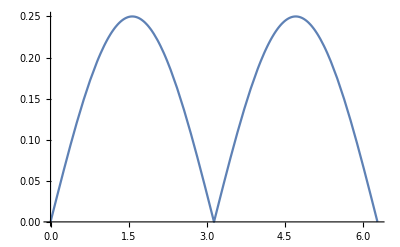

```mathematica
Plot[Abs[Sin[x]]/4,{x,0,2Pi}]
```

```mathematica
pdfDist=Piecewise[{{Abs[Sin[x]]/4,0≤ x≤ 2Pi}},0];
```

```mathematica
Plot[pdfDist,{x,0,2Pi}]
```

-Graphics-

```mathematica
cdfDist=Integrate[Abs[Sin[t]]/4,{t,0,x},Assumptions->x∈Reals]
```

ConditionalExpression[1/4 (1-Cos[x]), C[1]∈ℤ&&x<π&&x≥2 π C[1]&&C[1]≥0]

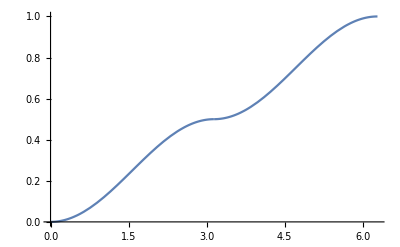

```mathematica
Plot[cdfDist,{x,0,2Pi}]
```